# 2-band chiral: self-consistency, Ds and Tc

### Def: bloch state

```mathematica
sigmax={{0,1},{1,0}};
sigmay={{0,-I},{I,0}};
sigmaz={{1,0},{0,-1}};
```

```mathematica
Clear[m]
```

```mathematica
ham=aa sigmax+bb sigmay+m sigmaz;
Eigensystem[ham]
```

{{-√(aa^2+bb^2+m^2),√(aa^2+bb^2+m^2)},{{-(-m+√(aa^2+bb^2+m^2))/(aa+ⅈ bb),1},{-(-m-√(aa^2+bb^2+m^2))/(aa+ⅈ bb),1}}}

```mathematica
a[J_,m_,k_,phi_]:=k^J Cos[J phi]
```

```mathematica
b[J_,m_,k_,phi_]:=k^J Sin[J phi]
```

Bloch states:

```mathematica
udisp[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)+2m Sqrt[a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2])^(-1/2){m+(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2),a[J,m,k,phi]+I b[J,m,k,phi]}
```

```mathematica
udispdag[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)+2m Sqrt[a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2])^(-1/2){m+(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2),a[J,m,k,phi]-I b[J,m,k,phi]}
```

```mathematica
uflat[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)+2m Sqrt[a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2])^(-1/2){m-(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2),a[J,m,k,phi]+I b[J,m,k,phi]}
```

```mathematica
uflatdag[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)+2m Sqrt[a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2])^(-1/2){m-(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2),a[J,m,k,phi]-I b[J,m,k,phi]}
```

```mathematica
Simplify[udisp[j,m,k,phi].udispdag[j,m,k,phi]]
```

1

```mathematica
Simplify[udisp[j,m,k,phi].uflatdag[j,m,k,phi]]
```

0

### Def: quantum metric

```mathematica
(* QM of the band*)
gxx[J_,m_,k_]:=J^2 k^(2J-2)(m^2+k^(2J)/2)/(4(m^2+k^(2J))^2)
```

### Def: dispersion, quasiparticle energy

```mathematica
Clear[J,m]
Simplify[a[J,m,k,phi]^2+b[J,m,k,phi]^2]
```

k^(2 J)

```mathematica
edisp[J_,m_,k_]:=2Sqrt[k^(2J)+m^2]
```

quasiparticle band at μ=0:

```mathematica
quasidisp[J_,m_,k_,delta_,mu_]:=Sqrt[(edisp[J,m,k]-mu)^2+delta^2]
```

```mathematica
quasiflat[J_,m_,k_,delta_,mu_]:=Sqrt[mu^2+delta^2]
```

## secant to solve gap equation

### Def: gap eq at T=0, to get U_A and U_B

compute U from the gap equation

```mathematica
ua2band[J_,m_]:=(
integral=(1/(2π)^2)NIntegrate[k (Abs[udisp[J,m,k,phi][[1]]]^2/(2quasidisp[J,m,k,delta,mu])+Abs[uflat[J,m,k,phi][[1]]]^2/(2quasiflat[J,m,k,delta,mu])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"];
1/integral
)
```

```mathematica
ub2band[J_,m_]:=(
integral=(1/(2π)^2)NIntegrate[k (Abs[udisp[J,m,k,phi][[2]]]^2/(2quasidisp[J,m,k,delta,mu])+Abs[uflat[J,m,k,phi][[2]]]^2/(2quasiflat[J,m,k,delta,mu])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"];
1/integral
)
```

### calculation

```mathematica
J=1;delta=0.02;mu=0;
mlist=Table[0.001(i-1)+0.0001,{i,1,51}];
ualist={};
ublist={};
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=ua2band[J,m];
ubvalue=ub2band[J,m];
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
];
dataA=Table[{2mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{2mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
```

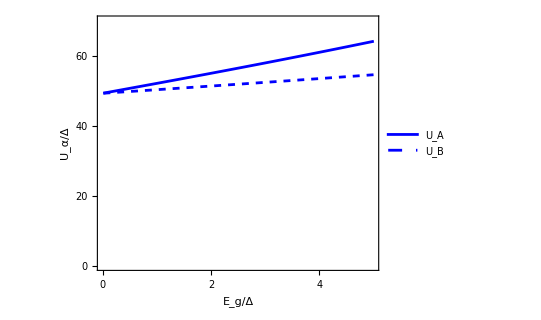

```mathematica
small2band=ListPlot[{dataA,dataB},Joined->True,PlotRange->{{0,5},{0,70}},
PlotStyle->{Blue,{Blue,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,
FrameTicks->{{{0,20,40,60},None},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ","U_α/Δ"},
PlotLegends->Placed[LineLegend[{Style["U_A",15],Style["U_B",15]},LegendLayout->"Row"], {0.35,0.93}],
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

```mathematica
J=1;delta=0.2;mu=0;
mlist=Table[0.01(i-1)+0.001,{i,1,51}];
ualist={};
ublist={};
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=ua2band[J,m];
ubvalue=ub2band[J,m];
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
];
dataA=Table[{2mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{2mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
```

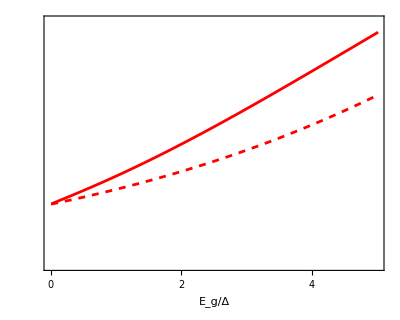

```mathematica
large2band=ListPlot[{dataA,dataB},Joined->True,PlotRange->{{0,5},{0,170}},
PlotStyle->{Red,{Red,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,FrameTicks->{{None,{0,50,100,150}},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ",""},
(*PlotLegends->Placed[{"U_A","U_B"}, {0.3,0.8}],*)
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

```mathematica
uplot2band=Overlay[{small2band,large2band}]
```

-Graphics--Graphics-

```mathematica
Export["2bandU.pdf",uplot2band]
```

2bandU.pdf

### Def: secant method solve Δ from fixed U_A, U_B at finite T

```mathematica
newtonA2band[deltaA_?NumericQ,deltaB_?NumericQ,temp_?NumericQ,uA_,uB_]:=(
deltaavg=(deltaA+deltaB)/2;
integral=(uA/(2π)^2)deltaavg NIntegrate[k (Abs[udisp[J,m,k,phi][[1]]]^2 Tanh[quasidisp[J,m,k,deltaavg,mu]/(2temp)]/(2quasidisp[J,m,k,deltaavg,mu])+Abs[uflat[J,m,k,phi][[1]]]^2Tanh[quasiflat[J,m,k,deltaavg,mu]/(2temp)]/(2quasiflat[J,m,k,deltaavg,mu])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaA
)
```

```mathematica
newtonB2band[deltaA_?NumericQ,deltaB_?NumericQ,temp_?NumericQ,uA_,uB_]:=(
deltaavg=(deltaA+deltaB)/2;
integral=(uB/(2π)^2)deltaavg NIntegrate[k (Abs[udisp[J,m,k,phi][[2]]]^2 Tanh[quasidisp[J,m,k,deltaavg,mu]/(2temp)]/(2quasidisp[J,m,k,deltaavg,mu])+Abs[uflat[J,m,k,phi][[2]]]^2Tanh[quasiflat[J,m,k,deltaavg,mu]/(2temp)]/(2quasiflat[J,m,k,deltaavg,mu])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaB
)
```

```mathematica
secant2bandstep[{deltaA0_,deltaB0_},{deltaA1_,deltaB1_}]:=(
input0={deltaA0,deltaB0};
input1={deltaA1,deltaB1};
functionlist={newtonA2band,newtonB2band};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],temp,uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],temp,uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],temp,uA,uB],{k,1,2}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
secant2band[inputdeltaA_,inputdeltaB_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB};
outputlist0=outputlist1+0.001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.95,secant2bandstep[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
)
```

### example calculation

m=0 is always uniform

```mathematica
J=1;mvalue=0;delta=0.1;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
temp=0.0001;m=0;
secant2band[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.078125,Null}

damping factor is 1.

deltas are {0.1,0.1}

```mathematica
J=1;mvalue=0;delta=0.1;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
temp=0.01;m=0;
secant2band[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.109375,Null}

damping factor is 0.999872

deltas are {0.099991,0.099991}

as m becomes larger

```mathematica
J=1;mvalue=0;delta=0.1;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
temp=0.01;m=0.1;
secant2band[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{2.21875,Null}

damping factor is 0.983645

deltas are {0.0613689,0.0789721}

```mathematica
J=1;mvalue=0;delta=0.1;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
temp=0.01;m=0.3;
secant2band[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{1.60938,Null}

damping factor is 0.975222

deltas are {0.0248751,0.049544}

```mathematica
J=1;mvalue=0;delta=0.1;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
temp=0.01;m=0.5;
secant2band[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{2.15625,Null}

damping factor is 0.959485

deltas are {0.00833485,0.0243205}

## Ds vs m plots (μ can be finite)

### Def: Ds for numerical (any ν):

```mathematica
(*the x direction has been averaged*)
vsquare[J_,m_,k_]:=2J^2k^(4J-2)/(m^2+k^(2J))
```

```mathematica
dsconv[J_?NumericQ,m_?NumericQ,delta_?NumericQ,mu_?NumericQ]:=NIntegrate[(k/(2π))(delta^2/quasidisp[J,m,k,delta,mu]^3)vsquare[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

```mathematica
dsgeo[J_?NumericQ,m_?NumericQ,delta_?NumericQ,mu_?NumericQ]:=NIntegrate[(k/(2π))(4delta^2/quasiflat[J,m,k,delta,mu]+4delta^2/quasidisp[J,m,k,delta,mu]-(8delta^2/(quasiflat[J,m,k,delta,mu]+quasidisp[J,m,k,delta,mu]))(1+(delta^2-mu(edisp[J,m,k]-mu))/(quasiflat[J,m,k,delta,mu]quasidisp[J,m,k,delta,mu])))gxx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

### calculation: Ds vs m, Δ=0.01, ν=0.5, numerical*

```mathematica
(*delta=0.01, filling=1/2*)
J=1;delta=0.01;
filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
```

```mathematica
(*SW total*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data001total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.25,Null}

```mathematica
(*SW geo*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data001geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.125,Null}

```mathematica
(*SW conv*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data001conv=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.078125,Null}

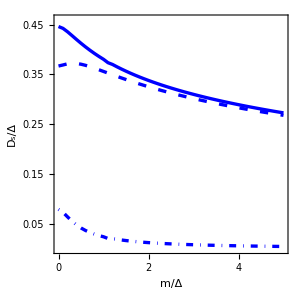

```mathematica
dsvsm=ListPlot[{data001total,data001geo,data001conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed}(*,{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}*)},PlotRange->{{0,5},{0,0.46}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1,ImageSize->300]
```

### Def: Ds for analytical (ν=0.5):

```mathematica
chi[λ_,κ_]:=Log[(1+Sqrt[1+κ^2])/(1+Sqrt[1+λ^2κ^2])]
```

```mathematica
F1geo[J_,λ_,κ_]:=(J/(8π))(2-λ^2κ^2)
```

```mathematica
F2geo[J_,λ_,κ_]:=(J/(8π))(1-λ^2-λ^2κ^2Log[λ]-Sqrt[1+λ^2κ^2]+λ^2Sqrt[1+κ^2])
```

```mathematica
F1conv[J_,λ_,κ_]:=(J/(4π))λ^2κ^2
```

```mathematica
F2conv[J_,λ_,κ_]:=(J/(4π))(λ^2κ^2Log[λ]+(1+λ^2κ^2)(1/Sqrt[1+λ^2κ^2]-1/Sqrt[1+κ^2]))
```

### calculation: Ds vs m, Δ=0.01, ν=0.5, analytical*

now compare with half-filling analytical using F functions:

```mathematica
(*delta=0.01, filling=1/2*)
J=1;delta=0.01;
filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
```

```mathematica
(*SW total*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
w=2Sqrt[1+m^2];
λ=2m/w;
κ=w/delta;
dstotvalue=(F1geo[J,λ,κ]+F1conv[J,λ,κ])chi[λ,κ]+(F2geo[J,λ,κ]+F2conv[J,λ,κ]);
AppendTo[dslist,dstotvalue];
]//Timing
data001totalanalytical=Table[{mlist[[j]]/delta,dslist[[j]]},{j,1,Length[mlist]}];
```

{0.,Null}

```mathematica
(*SW geo*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
w=2Sqrt[1+m^2];
λ=2m/w;
κ=w/delta;
dsgeovalue=F1geo[J,λ,κ]chi[λ,κ]+F2geo[J,λ,κ];
AppendTo[dslist,dsgeovalue];
]//Timing
data001geoanalytical=Table[{mlist[[j]]/delta,dslist[[j]]},{j,1,Length[mlist]}];
```

{0.,Null}

```mathematica
(*SW conv*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
w=2Sqrt[1+m^2];
λ=2m/w;
κ=w/delta;
dsconvvalue=F1conv[J,λ,κ]chi[λ,κ]+F2conv[J,λ,κ];
AppendTo[dslist,dsconvvalue];
]//Timing
data001convanalytical=Table[{mlist[[j]]/delta,dslist[[j]]},{j,1,Length[mlist]}];
```

{0.,Null}

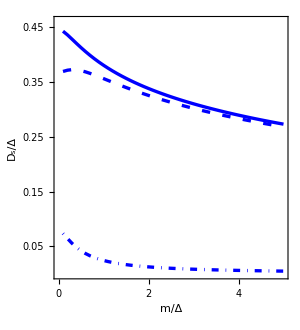

```mathematica
dsvsmanalytical=ListPlot[{data001totalanalytical,data001geoanalytical,data001convanalytical},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed}(*,{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}*)},PlotRange->{{0,5},{0,0.46}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->300]
```

### Def: Ds of finite temp

coherence factors between flat and dispersive band:

```mathematica
pvcplus[J_,m_,k_,deltat_,mu_]:=(1/2)(1+((-mu)(edisp[J,m,k]-mu)+deltat^2)/(quasiflat[J,m,k,deltat,mu]quasidisp[J,m,k,deltat,mu]))
```

```mathematica
pvcminus[J_,m_,k_,deltat_,mu_]:=(1/2)(1-((-mu)(edisp[J,m,k]-mu)+deltat^2)/(quasiflat[J,m,k,deltat,mu]quasidisp[J,m,k,deltat,mu]))
```

```mathematica
dstemp[J_?NumericQ,m_?NumericQ,deltat_?NumericQ,mu_?NumericQ,temp_?NumericQ]:=deltat^2 NIntegrate[(k/(2π))(vsquare[J,m,k]/quasidisp[J,m,k,deltat,mu]^3)(Tanh[quasidisp[J,m,k,deltat,mu]/(2temp)]-(quasidisp[J,m,k,deltat,mu]/(2temp))Sech[quasidisp[J,m,k,deltat,mu]/(2temp)]^2),{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]+4deltat^2NIntegrate[(k/(2π))(Tanh[quasiflat[J,m,k,deltat,mu]/(2temp)]/quasiflat[J,m,k,deltat,mu]+Tanh[quasidisp[J,m,k,deltat,mu]/(2temp)]/quasidisp[J,m,k,deltat,mu]-2pvcplus[J,m,k,deltat,mu](Tanh[quasiflat[J,m,k,deltat,mu]/(2temp)]+Tanh[quasidisp[J,m,k,deltat,mu]/(2temp)])/(quasiflat[J,m,k,deltat,mu]+quasidisp[J,m,k,deltat,mu])-2pvcminus[J,m,k,deltat,mu](Tanh[quasiflat[J,m,k,deltat,mu]/(2temp)]-Tanh[quasidisp[J,m,k,deltat,mu]/(2temp)])/(quasiflat[J,m,k,deltat,mu]-quasidisp[J,m,k,deltat,mu]))gxx[J,m,k],{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]
```

test the function dstemp (compare with the T=0 function dsconv+dsgeo):

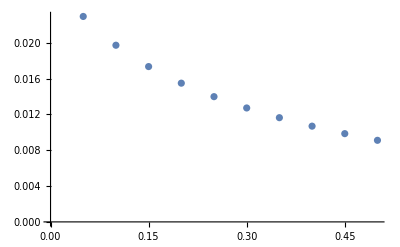

```mathematica
J=1;temp=0.0001;delta=0.1;mu=0;
ListPlot[Table[{0.05i,dsconv[J,0.05i,delta,mu]+dsgeo[J,0.05i,delta,mu]},{i,1,10}]]
```

```mathematica
J=1;temp=0.0001;delta=0.1;mu=0;
ListPlot[Table[{0.05i,dstemp[J,0.05i,delta,mu,temp]},{i,1,10}]]
```

-Graphics-

the two completely match! Now check mu=delta.

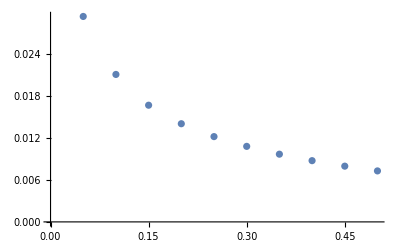

```mathematica
J=1;temp=0.0001;delta=0.1;mu=0.1;
ListPlot[Table[{0.05i,dsconv[J,0.05i,delta,mu]+dsgeo[J,0.05i,delta,mu]},{i,1,10}]]
```

```mathematica
J=1;temp=0.0001;delta=0.1;mu=0.1;
ListPlot[Table[{0.05i,dstemp[J,0.05i,delta,mu,temp]},{i,1,10}]]
```

-Graphics-

### J=1, Δ=0.01 ε_Λ and Δ=0.1 ε_Λ (μ=0)***

```mathematica
(*SW total, 0.02*)
J=1;delta=0.02;mu=0;
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data002total=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.25,Null}

```mathematica
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data002geo=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.171875,Null}

```mathematica
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data002conv=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.15625,Null}

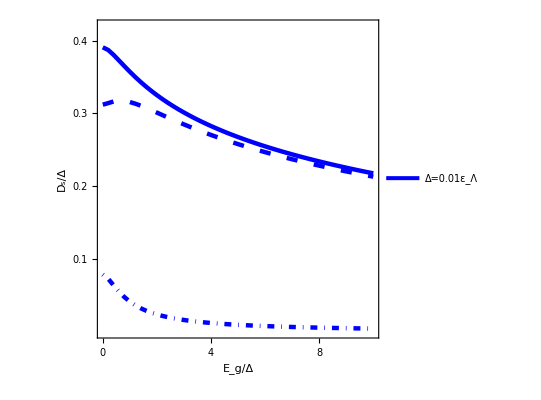

```mathematica
dsvsm001=ListPlot[{data002total,data002geo,data002conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed}},PlotRange->{{0,10},{0,0.42}},
Frame->True,FrameLabel->{Style["E_g/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[18],
PlotLegends->Placed[LineLegend[{Style["Δ=0.01ε_Λ",20]}],{0.70,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
(*SW total, 0.2*)
J=1;delta=0.2;mu=0;
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data02total=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.125,Null}

```mathematica
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data02geo=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.140625,Null}

```mathematica
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data02conv=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.046875,Null}

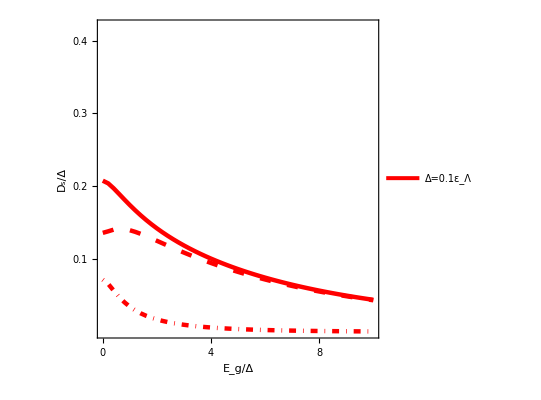

```mathematica
dsvsm01=ListPlot[{data02total,data02geo,data02conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}},PlotRange->{{0,10},{0,0.42}},
Frame->True,FrameLabel->{Style["E_g/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[18],
PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",20]}],{0.71,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
dsvsm=Overlay[{dsvsm001,dsvsm01}]
```

-Graphics--Graphics-

```mathematica
Export["dsvsm2band.pdf",dsvsm]
```

dsvsm2band.pdf

### J=2, Δ=0.01 ε_Λ and Δ=0.1 ε_Λ (μ=0)***

```mathematica
(*SW total, 0.02*)
J=2;delta=0.02;mu=0;
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data002total=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.21875,Null}

```mathematica
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data002geo=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.171875,Null}

```mathematica
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data002conv=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.109375,Null}

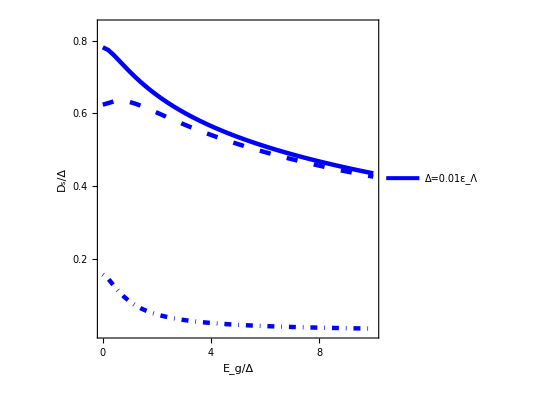

```mathematica
dsvsm001=ListPlot[{data002total,data002geo,data002conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed}},PlotRange->{{0,10},{0,0.84}},
Frame->True,FrameLabel->{Style["E_g/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.2,0.4,0.6,0.8},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[18],
PlotLegends->Placed[LineLegend[{Style["Δ=0.01ε_Λ",20]}],{0.70,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
(*SW total, 0.2*)
J=2;delta=0.2;mu=0;
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data02total=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.28125,Null}

```mathematica
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data02geo=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.203125,Null}

```mathematica
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data02conv=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.09375,Null}

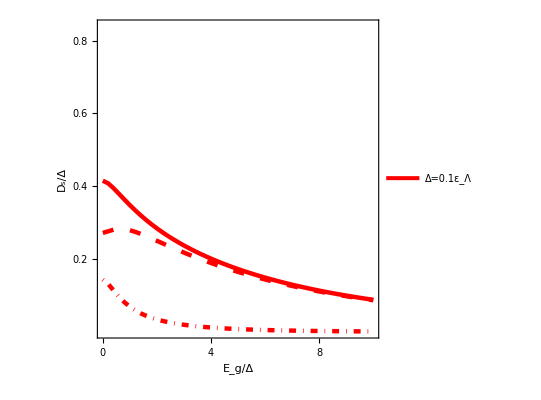

```mathematica
dsvsm01=ListPlot[{data02total,data02geo,data02conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}},PlotRange->{{0,10},{0,0.84}},
Frame->True,FrameLabel->{Style["E_g/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.2,0.4,0.6,0.8},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[18],
PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",20]}],{0.71,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
dsvsm=Overlay[{dsvsm001,dsvsm01}]
```

-Graphics--Graphics-

```mathematica
Export["dsvsm2band.pdf",dsvsm]
```

dsvsm2band.pdf

### J=6, Δ=0.01 ε_Λ and Δ=0.1 ε_Λ (μ=0)***

```mathematica
(*SW total, 0.02*)
J=6;delta=0.02;mu=0;
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data002total=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.09375,Null}

```mathematica
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data002geo=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.03125,Null}

```mathematica
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data002conv=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.109375,Null}

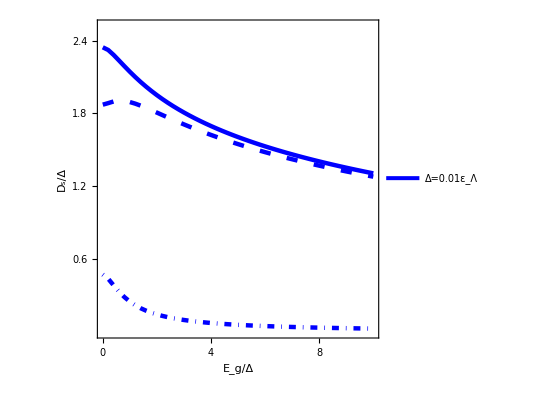

```mathematica
dsvsm001=ListPlot[{data002total,data002geo,data002conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed}},PlotRange->{{0,10},{0,2.52}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],Style["D_s/Δ",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.6,1.2,1.8,2.4},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
PlotLegends->Placed[LineLegend[{Style["Δ=0.01ε_Λ",18]}],{0.70,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
(*SW total, 0.2*)
J=6;delta=0.2;mu=0;
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data02total=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.078125,Null}

```mathematica
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data02geo=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.03125,Null}

```mathematica
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data02conv=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.046875,Null}

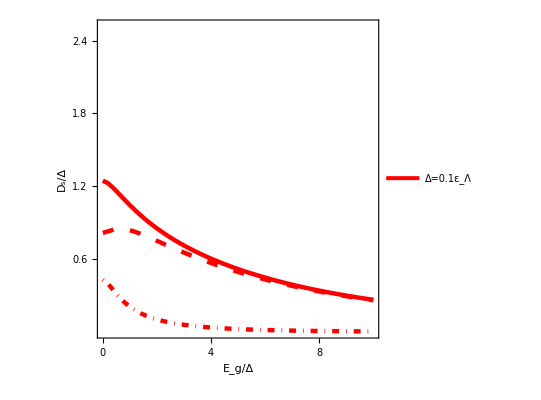

```mathematica
dsvsm01=ListPlot[{data02total,data02geo,data02conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}},PlotRange->{{0,10},{0,2.52}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],Style["D_s/Δ",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.6,1.2,1.8,2.4},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.71,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
dsvsm=Overlay[{dsvsm001,dsvsm01}]
```

-Graphics--Graphics-

```mathematica
Export["dsvsm2bandJ6.pdf",dsvsm]
```

dsvsm2bandJ6.pdf

### other calculations: Δ=0.01, ν=0.2, numerical

```mathematica
(*delta=0.01, filling=1/2*)
J=1;delta=0.01;
filling=0.2;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
```

```mathematica
mu
```

-0.0075

```mathematica
(*SW total*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data001total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.203125,Null}

```mathematica
(*SW geo*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data001geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.15625,Null}

```mathematica
(*SW conv*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data001conv=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.0625,Null}

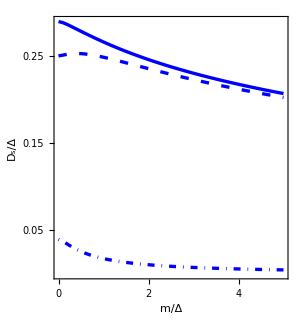

```mathematica
dsvsm=ListPlot[{data001total,data001geo,data001conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed}(*,{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}*)},(*PlotRange->{{0,5},{0,0.15}},*)
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->300]
```

### Δ=0.01, ν=0.2, analytical

now compare with half-filling analytical using F functions:

```mathematica
(*delta=0.01, filling=1/2*)
J=1;delta=0.01;
filling=0.2;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
deltaprime=2Sqrt[filling(1-filling)]delta;
```

```mathematica
(*SW total*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
w=2Sqrt[1+m^2];
λgeo=2m/w;
κgeo=w/delta;
λconv=(2m-mu)/w;
κconv=w/delta;
dstotvalue=(*2Sqrt[filling(1-filling)]*)(F1geo[J,λgeo,κgeo]chi[λgeo,κgeo]+F2geo[J,λgeo,κgeo])+F1conv[J,λconv,κconv]chi[λconv,κconv]+F2conv[J,λconv,κconv];
AppendTo[dslist,dstotvalue];
]//Timing
data001totalanalytical=Table[{mlist[[j]]/delta,dslist[[j]]},{j,1,Length[mlist]}];
```

{0.,Null}

```mathematica
(*SW geo*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
w=2Sqrt[1+m^2];
λgeo=2m/w;
κgeo=w/delta;
dsgeovalue=(*2Sqrt[filling(1-filling)]*)(F1geo[J,λgeo,κgeo]chi[λgeo,κgeo]+F2geo[J,λgeo,κgeo]);
AppendTo[dslist,dsgeovalue];
]//Timing
data001geoanalytical=Table[{mlist[[j]]/delta,dslist[[j]]},{j,1,Length[mlist]}];
```

{0.,Null}

```mathematica
(*SW conv*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
w=2Sqrt[1+m^2];
λconv=(2m-mu)/w;
κconv=w/delta;
dsconvvalue=F1conv[J,λconv,κconv]chi[λconv,κconv]+F2conv[J,λconv,κconv];
AppendTo[dslist,dsconvvalue];
]//Timing
data001convanalytical=Table[{mlist[[j]]/delta,dslist[[j]]},{j,1,Length[mlist]}];
```

{0.,Null}

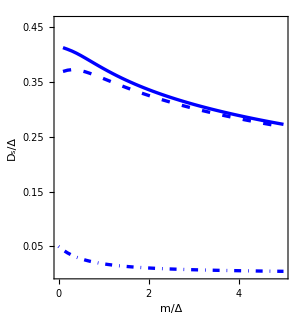

```mathematica
dsvsmanalytical=ListPlot[{data001totalanalytical,data001geoanalytical,data001convanalytical},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed}(*,{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}*)},PlotRange->{{0,5},{0,0.46}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->300]
```

### Δ=0.01, ν=0.05, numerical

```mathematica
(*delta=0.01, filling=1/2*)
J=1;delta=0.01;
filling=0.05;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
```

```mathematica
mu
```

-0.0206474

```mathematica
(*SW total*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data001total=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.328125,Null}

```mathematica
(*SW geo*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data001geo=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.203125,Null}

```mathematica
(*SW conv*)
mlist=Table[0.001(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data001conv=Table[{mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.0625,Null}

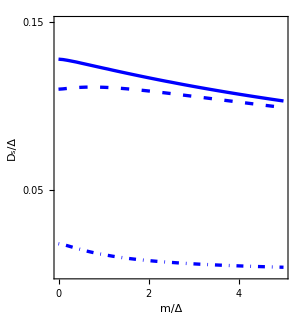

```mathematica
dsvsm=ListPlot[{data001total,data001geo,data001conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed}(*,{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}*)},PlotRange->{{0,5},{0,0.15}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["m/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45}},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->300]
```

### μ=-Δ scaling

```mathematica
(*SW total, 0.2*)
J=1;delta=0.2;mu=-delta;
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data02total=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.375,Null}

```mathematica
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data02geo=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.203125,Null}

```mathematica
mlist=Table[0.02(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data02conv=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.140625,Null}

```mathematica
(*SW total, 0.02*)
J=1;delta=0.02;mu=-delta;
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dstotvalue=dsconv[J,m,delta,mu]+dsgeo[J,m,delta,mu];
AppendTo[dslist,dstotvalue];
]//Timing
data002total=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.28125,Null}

```mathematica
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
data002geo=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.109375,Null}

```mathematica
mlist=Table[0.002(im-1),{im,1,51}];
dslist={};
For[im=1,im<Length[mlist]+1,im++,
m=mlist[[im]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
data002conv=Table[{2mlist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[mlist]}];
```

{0.03125,Null}

```mathematica
dsvsm=ListPlot[{data002total,data002geo,data002conv,data02total,data02geo,data02conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Blue,DotDashed},{Thickness[0.008],Red},{Thickness[0.008],Red,Dashing[{0.02,0.03}]},{Thickness[0.008],Red,DotDashed}},PlotRange->{{0,10},{0,0.4}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["E_g/Δ",20],Style["D_s/Δ",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4},{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4}},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01ε_Λ",18],Style["D_s^geo, Δ=0.01ε_Λ",18],Style["D_s^conv,Δ=0.01ε_Λ",18],Style["D_s,     Δ=0.1ε_Λ",18],Style["D_s^geo, Δ=0.1ε_Λ",18],Style["D_s^conv,Δ=0.1ε_Λ",18]}],{1.05,0.55}],
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->550]
```

-Graphics-

## 3-dim secant to find Tc

### Def: secant method

```mathematica
bkteq2band[deltaA_?NumericQ,deltaB_?NumericQ,temp_?NumericQ,uA_,uB_]:=(
deltaavg=(deltaA+deltaB)/2;
(π/8)dstemp[J,m,deltaavg,mu,temp]-temp
)
```

```mathematica
tc2bandstep[{deltaA0_,deltaB0_,temp0_},{deltaA1_,deltaB1_,temp1_}]:=(
input0={deltaA0,deltaB0,temp0};
input1={deltaA1,deltaB1,temp1};
functionlist={newtonA2band,newtonB2band,bkteq2band};
jacobian=ConstantArray[0,{3,3}];
For[i=1,i<4,i++,
For[j=1,j<4,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],changelist1[[3]],uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],input1[[3]],uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],input1[[3]],uA,uB],{k,1,3}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
tc2band[inputdeltaA_,inputdeltaB_,inputtemp_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB,inputtemp};
outputlist0=outputlist1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.98&&outputlist1[[3]]>tcmin,tc2bandstep[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
temp=outputlist1[[3]]
)
```

```mathematica
J=1;mvalue=0;delta=0.1;mu=0;tcmin=0.0001;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
m=0.1;temptrial=0.01;
tc2band[delta,delta,temptrial]//Timing
```

{1.78125,0.00564819}

### J=1, Δ=0.01ε_Λ and 0.1ε_Λ calculation***

```mathematica
{shape1,shape2}=Graphics/@{{Blue,Polygon[{{-0.5,0},{0.5,0},{0,√3/2}}]},{Red,Disk[{0,0},0.1]}};
```

```mathematica
J=1;mvalue=0;delta=0.02;mu=0;tcmin=0.0001;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
mlist=Table[0.0025(i-1)+0.0001,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.003;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,tc2band[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
temptrial=temp;
]//Timing
data001=Table[{2mlist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@mlist}];
```

{9.25,Null}

```mathematica
uA
uB
```

0.98579

0.98579

A useful function {#,ScientificForm@#}&/@

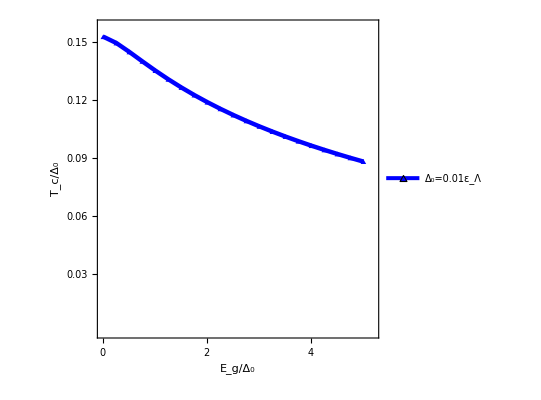

```mathematica
tc001=ListPlot[data001,
Joined->True,
PlotStyle->{{Blue,Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.158}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.03,0.06,0.09,0.12,0.15},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black,16],
PlotMarkers->{{shape1,0.035}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.01ε_Λ",16]}],{0.7,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
J=1;mvalue=0;delta=0.2;mu=0;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
mlist=Table[0.025(i-1)+0.001,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.02;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,tc2band[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
temptrial=temp;
]//Timing
data01=Table[{2mlist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@mlist}];
```

{26.6094,Null}

```mathematica
uA
uB
```

8.51238

8.51238

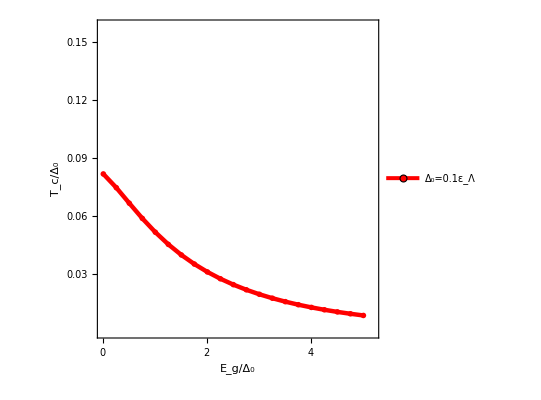

```mathematica
tc01=ListPlot[data01,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.158}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.03,0.06,0.09,0.12,0.15},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black,16],
PlotMarkers->{{shape2,0.03}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.1ε_Λ",16]}],{0.71,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
tcplot=Overlay[{tc001,tc01}]
```

-Graphics--Graphics-

```mathematica
Export["tc2bandJ1.pdf",tcplot]
```

tc2band.pdf

### J=6, Δ=0.01ε_Λ and 0.1ε_Λ calculation***

```mathematica
{shape1,shape2}=Graphics/@{{Blue,Polygon[{{-0.5,0},{0.5,0},{0,√3/2}}]},{Red,Disk[{0,0},0.1]}};
```

```mathematica
J=6;mvalue=0;delta=0.02;mu=0;tcmin=0.0001;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
mlist=Table[0.0025(i-1)+0.0005,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.008;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,tc2band[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
temptrial=temp;
]//Timing
data001=Table[{2mlist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@mlist}];
```

{250.906,Null}

```mathematica
uA
uB
```

0.775049

0.775049

A useful function {#,ScientificForm@#}&/@

```mathematica
data001
```

{{0.05,0.369486},{0.3,0.329167},{0.55,0.301884},{0.8,0.27706},{1.05,0.255385},{1.3,0.237469},{1.55,0.222849},{1.8,0.210743},{2.05,0.200493},{2.3,0.191633},{2.55,0.18384},{2.8,0.17689},{3.05,0.17062},{3.3,0.164911},{3.55,0.159672},{3.8,0.154832},{4.05,0.150336},{4.3,0.14614},{4.55,0.142251},{4.8,0.138547},{5.05,0.135051}}

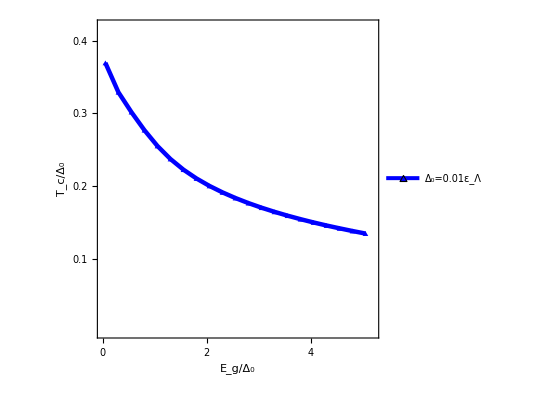

```mathematica
tc001=ListPlot[data001,
Joined->True,
PlotStyle->{{Blue,Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.42}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black,16],
PlotMarkers->{{shape1,0.035}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.01ε_Λ",16]}],{0.7,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
J=6;mvalue=0;delta=0.2;mu=0;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
mlist=Table[0.025(i-1)+0.005,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.1;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,tc2band[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
temptrial=temp;
]//Timing
data01=Table[{2mlist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@mlist}];
```

{88.3281,Null}

```mathematica
uA
uB
```

6.27966

6.27966

```mathematica
data01
```

{{0.05,0.28397},{0.3,0.22489},{0.55,0.176621},{0.8,0.132347},{1.05,0.101728},{1.3,0.0815473},{1.55,0.0673495},{1.8,0.0568238},{2.05,0.0485892},{2.3,0.0420033},{2.55,0.0366171},{2.8,0.0321362},{3.05,0.0283582},{3.3,0.0251386},{3.55,0.0223708},{3.8,0.0199743},{4.05,0.0178867},{4.3,0.0160588},{4.55,0.0144513},{4.8,0.0130323},{5.05,0.0117756}}

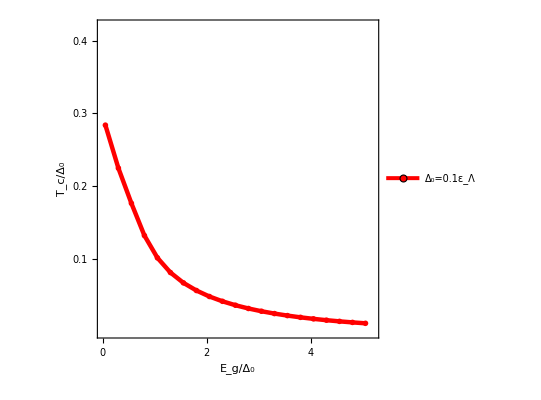

```mathematica
tc01=ListPlot[data01,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},PlotRange->{{0,5.2},{0,0.42}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black,16],
PlotMarkers->{{shape2,0.03}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.1ε_Λ",16]}],{0.71,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
tcplotj6=Overlay[{tc001,tc01}]
```

-Graphics--Graphics-

```mathematica
Export["tc2bandJ6.pdf",tcplotj6]
```

tc2bandJ6.pdf

## 2-dim secant to find T=0 SC gap vs Eg

the reason for this section is to show that for large J the Tc enhances

### Def: T=0 secant for SC gap

```mathematica
newtonA2bandt0[deltaA_?NumericQ,deltaB_?NumericQ,uA_,uB_]:=(
deltaavg=(deltaA+deltaB)/2;
(uA/(2π)^2)deltaavg NIntegrate[k (Abs[udisp[J,m,k,phi][[1]]]^2 /(2quasidisp[J,m,k,deltaavg,mu])+Abs[uflat[J,m,k,phi][[1]]]^2/(2quasiflat[J,m,k,deltaavg,mu])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaA
)
```

```mathematica
newtonB2bandt0[deltaA_?NumericQ,deltaB_?NumericQ,uA_,uB_]:=(
deltaavg=(deltaA+deltaB)/2;
(uB/(2π)^2)deltaavg NIntegrate[k (Abs[udisp[J,m,k,phi][[2]]]^2 /(2quasidisp[J,m,k,deltaavg,mu])+Abs[uflat[J,m,k,phi][[2]]]^2/(2quasiflat[J,m,k,deltaavg,mu])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaB
)
```

```mathematica
secant2bandstept0[{deltaA0_,deltaB0_},{deltaA1_,deltaB1_}]:=(
input0={deltaA0,deltaB0};
input1={deltaA1,deltaB1};
functionlist={newtonA2bandt0,newtonB2bandt0};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],uA,uB],{k,1,2}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
secant2bandt0[inputdeltaA_,inputdeltaB_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB};
outputlist0=outputlist1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.95&&inputdeltaA>0.0001,secant2bandstept0[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
)
```

### J=6, Δ=0.01ε_Λ and 0.1ε_Λ, T=0 SC gap vs Eg***

```mathematica
{shape1,shape2}=Graphics/@{{Blue,Polygon[{{-0.5,0},{0.5,0},{0,√3/2}}]},{Red,Disk[{0,0},0.1]}};
```

```mathematica
J=6;mvalue=0;delta=0.02;mu=0;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
mlist=Table[0.0025(i-1)+0.0005,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
deltaAlist={};
deltaBlist={};
deltalist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
secant2bandt0[deltaAtrial,deltaBtrial];
AppendTo[deltaAlist,deltaA];
AppendTo[deltaBlist,deltaB];
AppendTo[deltalist,(deltaA+deltaB)/2];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
]//Timing
data001=Table[{2mlist[[i]]/delta,deltalist[[i]]/delta},{i,1,Length@mlist}];
```

NIntegrate::levtime: Time spent solving linear system in LevinRule exceeded 10. seconds. Try increasing the value of the "TimeConstraint" option or decreasing the value of the "Points" option.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

{184.406,Null}

```mathematica
uA
uB
```

0.775049

0.775049

A useful function {#,ScientificForm@#}&/@

```mathematica
data001
```

{{0.05,0.888875},{0.3,0.789049},{0.55,0.72299},{0.8,0.666178},{1.05,0.618925},{1.3,0.58051},{1.55,0.549073},{1.8,0.524146},{2.05,0.501621},{2.3,0.482015},{2.55,0.464768},{2.8,0.449391},{3.05,0.435523},{3.3,0.422894},{3.55,0.411301},{3.8,0.400586},{4.05,0.390624},{4.3,0.381316},{4.55,0.372582},{4.8,0.364354},{5.05,0.356578}}

```mathematica
OverBar[Δ]
```

Δ̄

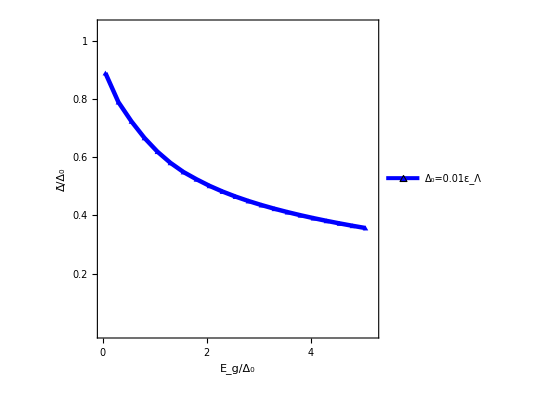

```mathematica
gap001=ListPlot[data001,
Joined->True,
PlotStyle->{{Blue,Thickness[0.008]}},PlotRange->{{0,5.2},{0,1.05}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["Δ̄/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black,16],
PlotMarkers->{{shape1,0.035}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.01ε_Λ",16]}],{0.7,0.93}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

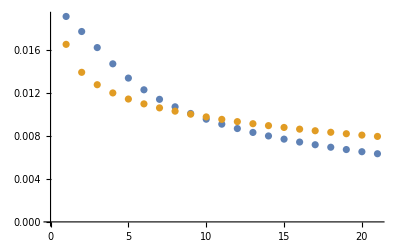

```mathematica
ListPlot[{deltaAlist,deltaBlist}]
```

```mathematica
J=6;mvalue=0;delta=0.2;mu=0;
uA=ua2band[J,mvalue];
uB=ub2band[J,mvalue];
mlist=Table[0.025(i-1)+0.001,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
deltaAlist={};
deltaBlist={};
deltalist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
secant2bandt0[deltaAtrial,deltaBtrial];
AppendTo[deltaAlist,deltaA];
AppendTo[deltaBlist,deltaB];
AppendTo[deltalist,(deltaA+deltaB)/2];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
]//Timing
data01=Table[{2mlist[[i]]/delta,deltalist[[i]]/delta},{i,1,Length@mlist}];
```

{36.2656,Null}

```mathematica
uA
uB
```

6.27966

6.27966

```mathematica
data01
```

{{0.01,0.882918},{0.26,0.642968},{0.51,0.509163},{0.76,0.389175},{1.01,0.306411},{1.26,0.251575},{1.51,0.21258},{1.76,0.183628},{2.01,0.161126},{2.26,0.143042},{2.51,0.128142},{2.76,0.115633},{3.01,0.104974},{3.26,0.0957824},{3.51,0.0877789},{3.76,0.0807526},{4.01,0.0745412},{4.26,0.0690174},{4.51,0.0640791},{4.76,0.059644},{5.01,0.0556443}}

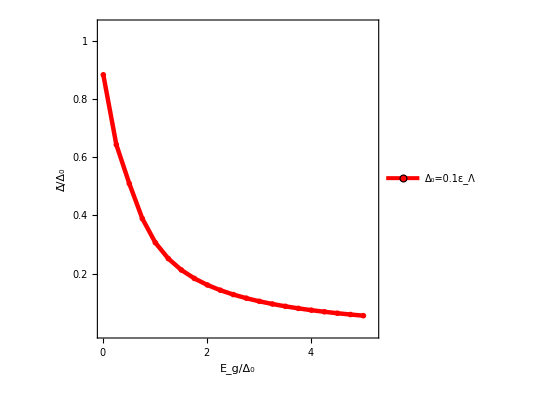

```mathematica
gap01=ListPlot[data01,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},PlotRange->{{0,5.2},{0,1.05}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["Δ̄/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[Black,16],
PlotMarkers->{{shape2,0.035}},
PlotLegends->Placed[LineLegend[{Style["Δ_0=0.1ε_Λ",16]}],{0.71,0.82}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
gap2bandj6=Overlay[{gap001,gap01}]
```

-Graphics--Graphics-

```mathematica
Export["gap2bandJ6.pdf",gap2bandj6]
```

gap2bandJ6.pdf

## Ds vs Δ***

### Ds vs delta numerical (ν=0.5)*

```mathematica
(*m=0.5*)
J=1;m=0.5;
filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
```

```mathematica
deltalist=Table[0.01(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam05geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.015625,Null}

```mathematica
deltalist=Table[0.01(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam05conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.03125,Null}

```mathematica
(*m=0.1*)
J=1;m=0.1;
filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
```

```mathematica
deltalist=Table[0.01(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam01geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.015625,Null}

```mathematica
deltalist=Table[0.01(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam01conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.078125,Null}

```mathematica
(*m=0*)
J=1;m=0;
filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
```

```mathematica
deltalist=Table[0.01(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam00geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.09375,Null}

```mathematica
deltalist=Table[0.01(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam00conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.0625,Null}

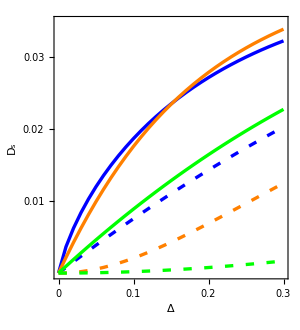

```mathematica
dsvsm=ListPlot[{datam00geo,datam00conv,datam01geo,datam01conv,datam05geo,datam05conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Orange},{Thickness[0.008],Orange,Dashing[{0.02,0.03}]},{Thickness[0.008],Green},{Thickness[0.008],Green,Dashing[{0.02,0.03}]}},PlotRange->{{0,0.3},{-0.0001,0.035}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["Δ",20],Style["D_s",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.01,0.02,0.03},None},{{0,0.1,0.2,0.3},None}},
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->300]
```

### Ds vs delta numerical (ν=0.05)*

```mathematica
(*m=0.5*)
J=1;m=0.5;
filling=0.05;
```

```mathematica
deltalist=Table[0.003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam05geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.03125,Null}

```mathematica
deltalist=Table[0.003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam05conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.0625,Null}

```mathematica
(*m=0.1*)
J=1;m=0.1;
filling=0.05;
```

```mathematica
deltalist=Table[0.003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam01geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.046875,Null}

```mathematica
deltalist=Table[0.003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam01conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.046875,Null}

```mathematica
(*m=0*)
J=1;m=0;
filling=0.05;
```

```mathematica
deltalist=Table[0.003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam00geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.0625,Null}

```mathematica
deltalist=Table[0.003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam00conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.109375,Null}

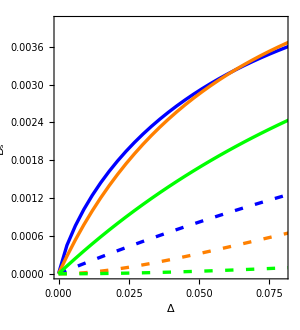

```mathematica
dsvsm=ListPlot[{datam00geo,datam00conv,datam01geo,datam01conv,datam05geo,datam05conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Orange},{Thickness[0.008],Orange,Dashing[{0.02,0.03}]},{Thickness[0.008],Green},{Thickness[0.008],Green,Dashing[{0.02,0.03}]}},PlotRange->{{0,0.08},{0,0.004}},
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["Δ",20],Style["D_s",20]},
FrameStyle->Directive[Thickness[0.007]],
(*FrameTicks->{{{0.01,0.02,0.03},None},{{0,0.1,0.2,0.3},None}},*)
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->300]
```

### Ds vs delta numerical (ν=0.001)*

```mathematica
(*m=0.5*)
J=1;m=0.5;
filling=0.001;
```

```mathematica
deltalist=Table[0.0003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam05geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.046875,Null}

```mathematica
deltalist=Table[0.0003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam05conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.109375,Null}

```mathematica
(*m=0.1*)
J=1;m=0.1;
filling=0.001;
```

```mathematica
deltalist=Table[0.0003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam01geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.15625,Null}

```mathematica
deltalist=Table[0.0003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam01conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.125,Null}

```mathematica
(*m=0*)
J=1;m=0;
filling=0.001;
```

```mathematica
deltalist=Table[0.0003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,dsgeovalue];
]//Timing
datam00geo=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.140625,Null}

```mathematica
deltalist=Table[0.0003(i-1)+0.00001,{i,1,31}];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,dsconvvalue];
]//Timing
datam00conv=Table[{deltalist[[j]],dslist[[j]]},{j,1,Length[deltalist]}];
```

{0.03125,Null}

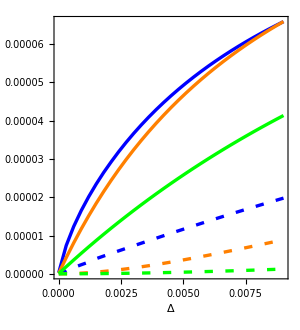

```mathematica
dsvsm=ListPlot[{datam00geo,datam00conv,datam01geo,datam01conv,datam05geo,datam05conv},
Joined->True,
PlotStyle->{{Thickness[0.008],Blue},{Thickness[0.008],Blue,Dashing[{0.02,0.03}]},{Thickness[0.008],Orange},{Thickness[0.008],Orange,Dashing[{0.02,0.03}]},{Thickness[0.008],Green},{Thickness[0.008],Green,Dashing[{0.02,0.03}]}},(*PlotRange->{{0,0.08},{0,0.004}},*)
(*PlotMarkers->{{m1,0.025},{Graphics[],0},{m2,0.025},{Graphics[],0},{m3,0.025},{Graphics[],0}},*)
Frame->True,FrameLabel->{Style["Δ",20],Style["D_s",20]},
FrameStyle->Directive[Thickness[0.007]],
(*FrameTicks->{{{0.01,0.02,0.03},None},{{0,0.1,0.2,0.3},None}},*)
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[LineLegend[{Style["D_s,     Δ=0.01W_d",18],Style["D_s^geo, Δ=0.01W_d",18],Style["D_s^conv,Δ=0.01W_d",18],Style["D_s,     Δ=0.1W_d",18],Style["D_s^geo, Δ=0.1W_d",18],Style["D_s^conv,Δ=0.1W_d",18]}],{1.05,0.55}],*)
(*PlotLegends->{Placed[LineLegend[{Style["D_s",20]}],{0.65,0.65}],Placed[LineLegend[{Style["D_s^geo",20]}],{0.65,0.55}]},*)
(*Epilog->{Text[Style["Δ=0.1W_d",20],{2.5,0.28}]},*)
AspectRatio->1.1,ImageSize->300]
```

```mathematica
mu
```

-0.142247

```mathematica
filling=0.05;
(2filling-1)/Sqrt[1-(2filling-1)^2]
```

-2.06474

### Def: analytical: twobandgeods, twobandconvds

```mathematica
twobandgeods[J_,m_,delta_]:=(
λ=m/Sqrt[1+m^2];
κ=2Sqrt[1+m^2]/delta;
delta(F1geo[J,λ,κ]chi[λ,κ]+F2geo[J,λ,κ])
)
```

```mathematica
twobandconvds[J_,m_,delta_]:=(
λ=m/Sqrt[1+m^2];
κ=2Sqrt[1+m^2]/delta;
delta(F1conv[J,λ,κ]chi[λ,κ]+F2conv[J,λ,κ])
)
```

```mathematica
0.1/Sqrt[1+0.1^2]
```

0.0995037

```mathematica
0.5/Sqrt[1+0.5^2]
```

0.447214

### Plot from analytical***

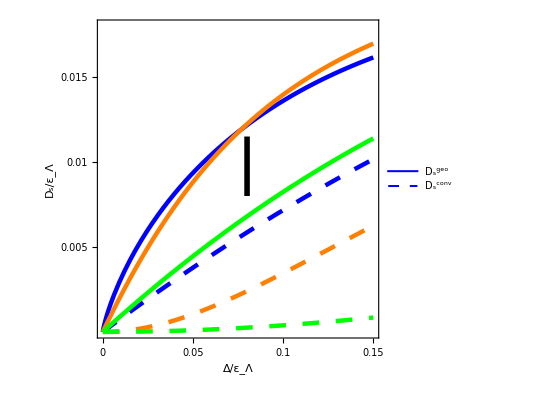

```mathematica
J=1;
ecutoff=2;
(*deltastar is delta in unit of ecutoff*)
twobanddssmall=Plot[{(*λ=0*)twobandgeods[J,0.00001,deltastar*ecutoff]/ecutoff,twobandconvds[J,0.00001,deltastar*ecutoff]/ecutoff,(*λ=0.1*)twobandgeods[J,0.1,deltastar*ecutoff]/ecutoff,twobandconvds[J,0.1,deltastar*ecutoff]/ecutoff,(*λ=0.5*)twobandgeods[J,0.5,deltastar*ecutoff]/ecutoff,twobandconvds[J,0.5,deltastar*ecutoff]/ecutoff(*twobandgeods[0.00001,delta]+twobandconvds[0.00001,delta],twobandgeods[0.1,delta]+twobandconvds[0.1,delta],twobandgeods[0.5,delta]+twobandconvds[0.5,delta]*)},{deltastar,0,0.15},PlotRange->{{0,0.15},{0,0.018}},
PlotStyle->{Directive[Blue,Thickness[0.008]],Directive[Blue,Thickness[0.008],Dashing[{0.03,0.03}]],Directive[Orange,Thickness[0.008]],Directive[Orange,Thickness[0.008],Dashing[{0.03,0.03}]],Directive[Green,Thickness[0.008]],Directive[Green,Thickness[0.008],Dashing[{0.03,0.03}]]},
LabelStyle->Directive[Black,25],
Frame->True,FrameLabel->{"Δ/ε_Λ","D_s/ε_Λ"},FrameTicks->{{{0.005,0.01,0.015},None},{{0,0.05,0.1,0.15},None}},
FrameStyle->Directive[Thickness[0.008]],PlotLegends->Placed[LineLegend[{Style["D_s^geo",20],Style["D_s^conv",20](*,Style["m=0.1, D_s^geo",25],Style["m=0.1, D_s^conv",25],Style["m=0.5, D_s^geo",25],Style["m=0.5, D_s^conv",25]*)}(*,LegendMarkerSize->22*)],{0.3,0.8}],
Epilog->{Thickness[0.01],Arrowheads[0.06],Arrow[{{0.08,0.008},{0.08,0.0115}}]},
AspectRatio->1,ImageSize->400]
```

```mathematica
Export["twobanddssmall.pdf",twobanddssmall]
```

twobanddssmall.pdf

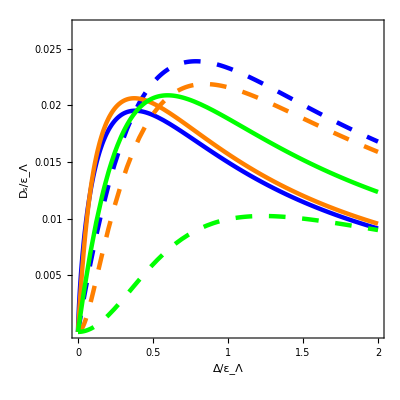

```mathematica
J=1;
ecutoff=2;
(*deltastar is delta in unit of ecutoff*)
twobanddslarge=Plot[{(*λ=0*)twobandgeods[J,0.00001,deltastar*ecutoff]/ecutoff,twobandconvds[J,0.00001,deltastar*ecutoff]/ecutoff,(*λ=0.1*)twobandgeods[J,0.1,deltastar*ecutoff]/ecutoff,twobandconvds[J,0.1,deltastar*ecutoff]/ecutoff,(*λ=0.5*)twobandgeods[J,0.5,deltastar*ecutoff]/ecutoff,twobandconvds[J,0.5,deltastar*ecutoff]/ecutoff(*twobandgeods[0.00001,delta]+twobandconvds[0.00001,delta],twobandgeods[0.1,delta]+twobandconvds[0.1,delta],twobandgeods[0.5,delta]+twobandconvds[0.5,delta]*)},{deltastar,0,2},PlotRange->{{0,2},{0,0.027}},
PlotStyle->{Directive[Blue,Thickness[0.008]],Directive[Blue,Thickness[0.008],Dashing[{0.03,0.03}]],Directive[Orange,Thickness[0.008]],Directive[Orange,Thickness[0.008],Dashing[{0.03,0.03}]],Directive[Green,Thickness[0.008]],Directive[Green,Thickness[0.008],Dashing[{0.03,0.03}]]},
LabelStyle->Directive[Black,25],
Frame->True,FrameLabel->{"Δ/ε_Λ","D_s/ε_Λ"},FrameTicks->{{{0.005,0.01,0.015,0.02,0.025},None},{{0,0.5,1,1.5,2},None}},
FrameStyle->Directive[Thickness[0.008]],(*PlotLegends->Placed[LineLegend[{Style["m=0, D_s^geo",25],Style["m=0, D_s^conv",25],Style["m=0.1, D_s^geo",25],Style["m=0.1, D_s^conv",25],Style["m=0.5, D_s^geo",25],Style["m=0.5, D_s^conv",25]}],{1,0.55}],*)
AspectRatio->1,ImageSize->400]
```

```mathematica
Export["twobanddslarge.pdf",twobanddslarge]
```

twobanddslarge.pdf

### crossover schematic*

```mathematica
colors=ColorData["Rainbow"]/@Subdivide[0,1,20]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.3386556, 0.6276854, 0.6832816],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.446557, 0.7074632, 0.5203932],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.5888042, 0.7409584, 0.37500680000000003],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.7408424, 0.7340177999999999, 0.2838318],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.9021174, 0.5055088, 0.2018252],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.8739574, 0.2607876, 0.15481040000000001],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
mtable=Table[0.15(i-1),{i,1,20}];
datatable={};
deltalist=Table[0.05(i-1)+0.00001,{i,1,151}];
J=1;filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
For[whichm=1,whichm<Length@mtable+1,whichm++,
m=mtable[[whichm]];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,{delta,dsgeovalue}];
];
AppendTo[datatable,dslist];
]
```

```mathematica
dsvsmgeo=ListPlot[datatable,
Joined->True,
PlotRange->{{0,4.5},{0,0.045}},
PlotStyle->colors,
Frame->True,FrameLabel->{Style["Δ",20],Style["D_s^geo",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.01,0.02,0.03,0.04},None},{{0,1,2,3,4},None}},
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[BarLegend["Rainbow",(*LegendLabel->"E_g",*)LegendMarkerSize->140],{1.01,0.6}],
AspectRatio->1,ImageSize->350]
```

-Graphics-

```mathematica
Export["dsvsmgeonew.pdf",dsvsmgeo]
```

dsvsmgeonew.pdf

```mathematica
mtable=Table[0.15(i-1),{i,1,20}];
datatable={};
deltalist=Table[0.05(i-1)+0.00001,{i,1,151}];
J=1;filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
For[whichm=1,whichm<Length@mtable+1,whichm++,
m=mtable[[whichm]];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,{delta,dsconvvalue}];
];
AppendTo[datatable,dslist];
]
```

```mathematica
dsvsmconv=ListPlot[datatable,
Joined->True,
PlotRange->{{0,4.5},{0,0.05}},
PlotStyle->colors,
Frame->True,FrameLabel->{Style["Δ",20],Style["D_s^conv",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.01,0.02,0.03,0.04},None},{{0,1,2,3,4},None}},
LabelStyle->Directive[Black, 20],
PlotLegends->Placed[BarLegend["Rainbow",(*LegendLabel->"E_g",*)LegendMarkerSize->140],{1.01,0.6}],
AspectRatio->1,ImageSize->350]
```

-Graphics-

```mathematica
Export["dsvsmconvnew.pdf",dsvsmconv]
```

dsvsmconvnew.pdf

### crossover schematic*(yafis version)

```mathematica
colors=ColorData["Rainbow"]/@Subdivide[0,1,5]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
mtable=Table[(i-1),{i,1,6}];
datatable={};
deltalist=Table[0.05(i-1)+0.00001,{i,1,161}];
J=1;filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
For[whichm=1,whichm<Length@mtable+1,whichm++,
m=mtable[[whichm]];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,{delta,dsgeovalue}];
];
AppendTo[datatable,dslist];
]
```

```mathematica
dsvsmgeo=Show[{ListPlot[datatable,
Joined->True,
PlotRange->{{0,8},{0,0.045}},
PlotStyle->colors,
Frame->True,FrameLabel->{Style["Δ",20],Style["D_s^geo",20]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.01,0.02,0.03,0.04},None},{{0,1,2,3,4,5,6,7,8},None}},
LabelStyle->Directive[Black, 16],
PlotLegends->Placed[BarLegend[{"Rainbow",{0,3}},5,LegendLabel->"E_g",LegendMarkerSize->140],{1.01,0.6}],
AspectRatio->0.7,ImageSize->350],Plot[0.05x,{x,0,8},PlotRange->{{0,8},{0,0.045}},
PlotStyle->{Dashed,Black}],Plot[0.125/x,{x,0,8},PlotRange->{{0,8},{0,0.045}},
PlotStyle->{Dashed,Black}]}]
```

-Graphics-

```mathematica
Export["dsvsmgeo2.pdf",dsvsmgeo]
```

dsvsmgeo2.pdf

```mathematica
colors2=ColorData["Rainbow"]/@Subdivide[0,1,5]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
mtable=Table[(i-1),{i,1,6}];
datatable={};
deltalist=Table[0.05(i-1)+0.00001,{i,1,161}];
J=1;filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
For[whichm=1,whichm<Length@mtable+1,whichm++,
m=mtable[[whichm]];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,{delta,dsconvvalue}];
];
AppendTo[datatable,dslist];
]
```

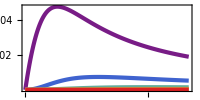

```mathematica
dsvsmconv=ListPlot[datatable,
Joined->True,
PlotRange->{{0,1},{0,0.03}},
PlotStyle->Table[{colors2[[ci]],Thickness[0.015]},{ci,1,Length@colors2}],
Frame->True,(*FrameLabel->{"",Style["D_s^conv",20]},*)
FrameStyle->Directive[Thickness[0.01],Black],
FrameTicks->{{{0.02,0.04},None},{{0,2,4,6,8},None}},
LabelStyle->Directive[Black, 20],
(*PlotLegends->Placed[BarLegend["Rainbow",(*LegendLabel->"E_g",*)LegendMarkerSize->140],{1.01,0.6}],*)
AspectRatio->0.5,ImageSize->200]
```

```mathematica
Export["dsvsmconv2.pdf",dsvsmconv]
```

dsvsmconv2.pdf

### crossover schematic***(new version)

```mathematica
colors=ColorData["Rainbow"]/@Subdivide[0,1,7]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.24882857142857143, 0.264202, 0.7825611428571428],RGBColor[0.2888631428571429, 0.5431845714285714, 0.7666072857142857],RGBColor[0.41993314285714284, 0.6952647142857142, 0.555374],RGBColor[0.6215634285714287, 0.743557, 0.3500992857142857],RGBColor[0.8241045714285714, 0.6995635714285714, 0.25042971428571426],RGBColor[0.9023275714285715, 0.49078171428571427, 0.199022],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
mtable=Table[0.75(i-1),{i,1,8}];
datatable={};
deltalist=Table[0.05(i-1)+0.00001,{i,1,161}];
J=1;filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
For[whichm=1,whichm<Length@mtable+1,whichm++,
m=mtable[[whichm]];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsgeovalue=dsgeo[J,m,delta,mu];
AppendTo[dslist,{delta,100dsgeovalue}];
];
AppendTo[datatable,dslist];
](*here times 100*)
```

```mathematica
dsvsmgeo=Show[{ListPlot[datatable,
Joined->True,
PlotRange->{{0,8},{0,5}},
PlotStyle->colors,
Frame->True,FrameLabel->{Style["Δ",16],Style["D_s^geo",16]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{1,2,3,4},None},{{0,1,2,3,4,5,6,7,8},None}},
LabelStyle->Directive[16],
PlotLegends->Placed[BarLegend[{"Rainbow",{0,3}},7,LegendLabel->Style["E_g",15],LegendMarkerSize->140],{1.01,0.6}],
AspectRatio->0.7,ImageSize->400],Plot[6x,{x,0,0.6},PlotRange->{{0,8},{0,4.5}},
PlotStyle->{Dashed,Black}],Plot[12/x,{x,4.2,8},PlotRange->{{0,8},{0,4.5}},
PlotStyle->{Dashed,Black}]}]
```

-Graphics-

```mathematica
Export["dsvsmgeo3.pdf",dsvsmgeo]
```

dsvsmgeo3.pdf

```mathematica
colors2=ColorData["Rainbow"]/@Subdivide[0,1,7]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.24882857142857143, 0.264202, 0.7825611428571428],RGBColor[0.2888631428571429, 0.5431845714285714, 0.7666072857142857],RGBColor[0.41993314285714284, 0.6952647142857142, 0.555374],RGBColor[0.6215634285714287, 0.743557, 0.3500992857142857],RGBColor[0.8241045714285714, 0.6995635714285714, 0.25042971428571426],RGBColor[0.9023275714285715, 0.49078171428571427, 0.199022],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
mtable=Table[0.75(i-1),{i,1,8}];
datatable={};
deltalist=Table[0.05(i-1)+0.00001,{i,1,161}];
J=1;filling=0.5;
mu=(2filling-1)delta/Sqrt[1-(2filling-1)^2];
For[whichm=1,whichm<Length@mtable+1,whichm++,
m=mtable[[whichm]];
dslist={};
For[i=1,i<Length[deltalist]+1,i++,
delta=deltalist[[i]];
dsconvvalue=dsconv[J,m,delta,mu];
AppendTo[dslist,{delta,100dsconvvalue}];
];
AppendTo[datatable,dslist];
]
```

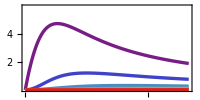

```mathematica
dsvsmconv=ListPlot[datatable,
Joined->True,
PlotRange->{{0,8},{0,6}},
PlotStyle->Table[{colors2[[ci]],Thickness[0.012]},{ci,1,Length@colors2}],
Frame->True,(*FrameLabel->{"",Style["D_s^conv",20]},*)
FrameStyle->Directive[Thickness[0.01],Black],
FrameTicks->{{{2,4},None},{{0,2,4,6,8},None}},
LabelStyle->Directive[15],
(*PlotLegends->Placed[BarLegend["Rainbow",(*LegendLabel->"E_g",*)LegendMarkerSize->140],{1.01,0.6}],*)
AspectRatio->0.5,ImageSize->200]
```

```mathematica
Export["dsvsmconv3.pdf",dsvsmconv]
```

dsvsmconv3.pdf